Ivan Gridelli 2028121

# Pendulum with oscillating support

## Theory

Let f(t) be the periodic (of period T) function describing the motion of the support on the z axis.
The coordinates of the mass are P:( x = l*sin(θ); y = 0; z = f(t)-l*cos(θ) ) from which we can get Ṗ to find T and U and hence determine the Lagrangian L = T - U.
We then wrote the equations of motion ∂_t (∂_(θ̇) L) - ∂_θ L = 0  getting θ^(..) = -(f''(t)+g)/lsin(θ).
We will study this system using the coordinates (θ,v) ∈ M = S^1×ℝ
We study the case where f(t) = a cos(Ωt) hence we get (up to a reparametrization of the time) θ^(..) = -(-a/lcos(t)+g/(l Ω^2))sin(θ)   i.e.    
								θ^(..) = -(α^2-K cos(t))sin(θ)                where K := a/l>=0 and α := ω/Ω>0  where ω := √(g/l)
This system in (θ,v) has two equilibria: z_- = (0,0) and z_+ = (π,0) called lower and upper equilibria.
We pass to the Reduced Extended Phase Space, where the two equilibria generate two periodic orbits whose stability can be studied by looking to the associated intersections with the Poincarè Map. 
The Poincarè Map is ψ : Σ_0 = M×{0} → Σ_0 that (z,0)→( PSM(z) = ϕ_(T,0)(z), 0) hence we can just study the Period Shift Map.
To study the stability we look to Spec(ψ ’(z_±) ) where the linearization can be solved using the variational equation U̇(t) = X’(z_±) U(t), U(0)=Id where
X’(θ,v) = (0 | 1
-(α^2-K cos(t))cos(θ) | 0)       hence, since they are fixed for the flow       X’(z_±) = (0 | 1
±(α^2-K cos(t)) | 0) 
Hence we can just solve two differential equations of the form x^(..)=±(α^2-K cos(t)) x with initial conditions (x(0),ẋ(0)) = (1,0) and (0,1)
Another choice for the Lagrangian  is L=1/2 OverDot[θ^2]-(α^2-K cos(t))cos(θ) fro which
the Legendre transformation has coordinates q=θ and p=∂_(θ̇) L=θ̇ hence its the identity. So the equations we are studying are actually Hamilton equations in our state space.
Hence the flow is symplectic and of determinant +1 (‘volume preserving’) and so in particular the linearization of the Poincarè Map is symplectic with determinant +1.
If we denote with {λ_+,λ_-} the spectrum of the linearization of the P.M.  there are three cases (if both are real then since the product is +1 they are in either situation 1 or 3, and if they are complex they are complex conjugates and so in case 2) which can be distinguished using the trace of the matrix:
-Graphics-
Case 1 means z_± is Lyapunov-unstable whereas cases 2 and 3 mean they are spectrally stable. (Moreover, recall that we cannot have asymptotic stability).
Let us find out, by varying the parameters α,K when they are unstable and spectrally stable.

## Lower Equilibrium

## Functions

### Functions to build the instability region

```mathematica
AlgoLCLower= Compile[  {{αk,_Real,1},  h  ,  {txu,_Real,1}  }  ,{h+txu⟦1⟧,txu⟦2⟧+h (txu⟦3⟧+1/2 h txu⟦2⟧ (-αk⟦1⟧^2+Cos[txu⟦1⟧] αk⟦2⟧)),txu⟦3⟧+h (txu⟦2⟧+1/2 h txu⟦3⟧) (-αk⟦1⟧^2+Cos[h/2+txu⟦1⟧] αk⟦2⟧)}]
```

CompiledFunction[…]

```mathematica
SolEqVarCLower=Compile[{{αk,_Real,1},{ndiv,_Integer},{xv,_Real,1}},
     Drop[     Nest[ AlgoLCLower[ αk,  (2Pi)/ndiv ,#]&, Prepend[xv,0], ndiv] ,  1] ]
```

CompiledFunction[…]

```mathematica
LinPSMCLower[ ak_ , ndiv_]:={  SolEqVarCLower[ak,ndiv,{1,0}]  ,  SolEqVarCLower[ak,ndiv,{0,1}]  }
```

```mathematica
TrLinLower[αk_,ndiv_]:=Abs[Tr[LinPSMCLower[αk,ndiv]]]
```

```mathematica
αkTrLinLower[{a_,k_} ,ndiv_]:= { a , k, TrLinLower[{a,k},ndiv] }
```

```mathematica
selLower[lst_]:=Select[lst,#[[-1]]>2&]
```

```mathematica
SezLower[lst_]:=Map[Drop[#,-1]&,selLower[lst]]
```

```mathematica
RandTrLinLower[npts_,ndiv_,αint_, kint_]:=ParallelTable[αkTrLinLower[{RandomReal[αint],RandomReal[kint]},ndiv],npts]
```

```mathematica
InstaReg[lst_,αint_, kint_]:=ListPlot[(Drop[#1,-1]&)/@selLower[lst],PlotRange->{αint,kint},PlotStyle->PointSize[0.005]]
```

### Functions for the animation of the pendulum

```mathematica
X[{α_,k_}][{t_,x_,v_}]:= {1,v, -(α^2-k Cos[t])Sin[x] } ;
mod[{t_,x_,v_}]:={Mod[t,2Pi],Mod[x,2Pi],v } ;
Algo[αk_,h_][z_]:=mod[   z+h X[αk][z+h/2 X[αk][z]]  ] ;
Orb[z_,αk_,h_,T_]:=NestList[ Algo[αk,h],z,Floor[T/h]] ;
pen[k_][{t_,θ_,v_}]:={{0,k Cos[t]},{Sin[θ],k Cos[t]-Cos[θ]}} ;
gpen[k_][txv_]:=Show[   Graphics[ {Thickness[.03], Line[  pen[k][txv] ]}  ]   ,PlotRange->{{-2,2},{-2,2}} ,  Axes->True,Ticks->None  ] ;
motion[{x_,v_},{α_,k_},{h_,T_},r_]:=Module[{mgpen},
  mgpen= Map[  gpen[k], Orb[{0,x,v},{α,k},h,T]];
  Animate[mgpen[[n]] ,{n,1,Length[mgpen],1}, AnimationRate->r]]
```

### Functions for the period shift map (or Poincaré Map)

```mathematica
AlgoCLower= Compile[  {{αk,_Real,1},  h  ,  {tθv,_Real,1}  }  ,{Mod[h+tθv⟦1⟧,2 π],Mod[tθv⟦2⟧+h (tθv⟦3⟧+1/2 h (-αk⟦1⟧^2+Cos[tθv⟦1⟧] αk⟦2⟧) Sin[tθv⟦2⟧]),2 π,-π],tθv⟦3⟧+h (-αk⟦1⟧^2+Cos[h/2+tθv⟦1⟧] αk⟦2⟧) Sin[tθv⟦2⟧+1/2 h tθv⟦3⟧]}]
```

CompiledFunction[…]

```mathematica
PSMCLower=Compile[{{αk,_Real,1},{ndiv,_Integer},{θv,_Real,1} },
     Drop[ Nest[ AlgoCLower[ αk,  (2Pi)/ndiv ,#]&, Prepend[θv,0], ndiv] ,  1] ]
```

CompiledFunction[…]

```mathematica
OrbPSMCLower[θv_,nit_,αk_,ndiv_]:= NestList[PSMCLower[αk,ndiv,#]&,θv,nit]
```

Here too, allow the possibility of changing the PlotRange:

```mathematica
GOrbPSMLower[θv_,nit_,αk_,ndiv_,plrg_]:= ListPlot[ OrbPSMCLower[θv,nit,αk,ndiv], PlotRange->plrg,PlotStyle->PointSize[.005]]
```

## Analysis of the instability region

Firstly let us plot the instability region:

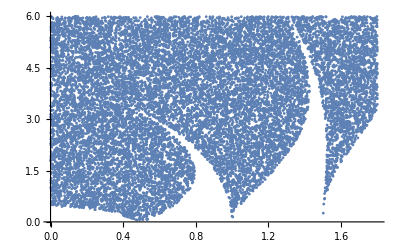

```mathematica
pts = RandTrLinLower[10000,400,{0,1.8},{0,6}]  ;
pts = Union[pts,RandTrLinLower[10000,400,{0,1.8},{0,6}]  ];
InstaReg[ pts,{0,1.8},{0,6}  ]
```

The instability region appears to be composed of several different tongues. How many are they? Where are they?  Let us plot  the absolute value of the trace of the linearization on the line k =0.01 and highlight in red when it reaches values above 2.

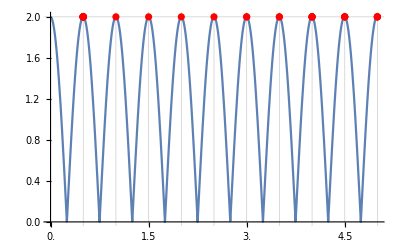

```mathematica
k=0.01;
line = Map[{#,k}&,Range[0,5,0.001]];
selected =Map[Drop[#,-1]&,selLower[Map[αkTrLinLower[#,1000]&,line]]];
selected=Map[#+{0,2-k}&,selected];
Show[Plot[TrLinLower[{α,k},400],{α,0,5},GridLines->{Range[0,5,0.5],{2}},Ticks->{Range[0,5,0.5],Automatic}],ListPlot[selected,PlotStyle-> Red]]
```

Each red segment corresponds to values of α such that (α,k=0.01) belongs to an instability region. We can see that we have separate ‘pieces’ of instability regions each corresponding to an half integer. This hints towards the existence of infinitely many tongues, one for every half integer.

### How do they touch the axis?

By enhancing the precision we can see that the end of the first tongue becomes ‘pointier’, suggesting that the region does not end in a whole area of contact with the axis, but only a single point. The same evaluation yields the same results for the other tongues.

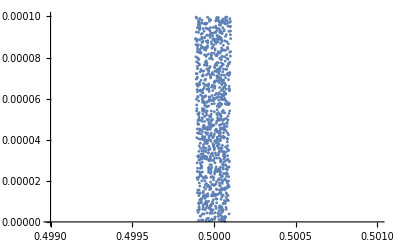
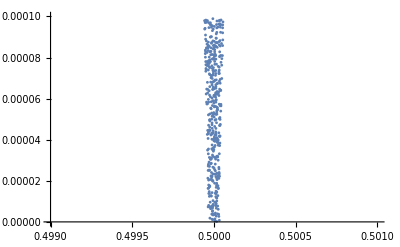
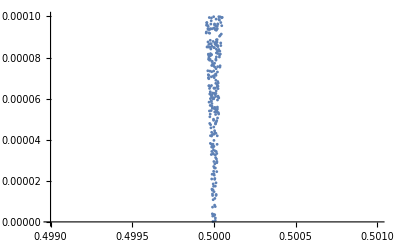

```mathematica
{InstaReg[RandTrLinLower[10000,400,{0.499,.501},{0,.0001}] ,{0.499,.501},{0,.0001}],
InstaReg[RandTrLinLower[10000,800,{0.499,.501},{0,.0001}] ,{0.499,.501},{0,.0001}],
InstaReg[RandTrLinLower[10000,1600,{0.499,.501},{0,.0001}] ,{0.499,.501},{0,.0001}]}
```

This result can also be determined analytically, since for k=0 the equations that determine the trace of the linearization become x^(..)=-α^2x with initial conditions (x(0),ẋ(0)) = (1,0) and (0,1) whose solutions are 
( x(t)=x_0cos(αt)+v_0/αsin(αt) ; v(t)=αx_0sin(αt)+v_0cos(αt) ) 
Hence  |Trace| = 2|cos(2πα)| ≤ 2. 
It equals 2 for every α=m/2 for m∈Z. By continuity we know that the frontier of the tongues is where the absolute value of the trace equals 2, and with what we have previously seen (for k>0 we always can find red intersections of the instability tongues with the line y=k, as k goes to zero) we can say that the instability region is made up of tongues that end in a cusp which ‘touches’ the axis k=0 at every half integer.
Hence we can deduce that for k=0 the lower equilibrium is stable and for all values of α ≠n/2  the equilibrium also admits a neighbourhood of values (α,k) for which it continues to be spectrally stable.

### What angle do they form? Are these cusps?

Let us see what happens to the tongues for values of k very small (very close to the axis):

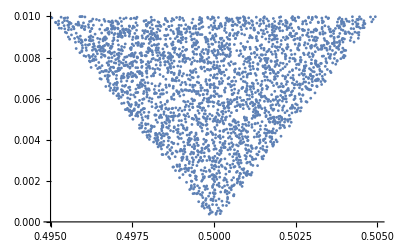
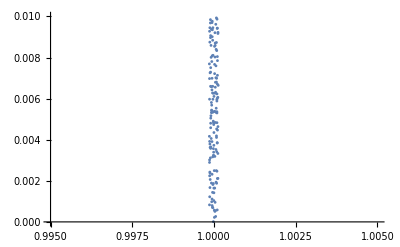
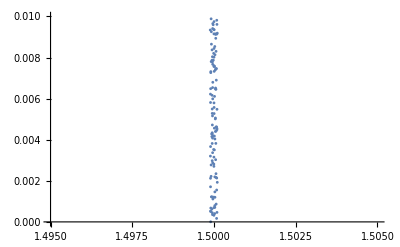

```mathematica
{InstaReg[RandTrLinLower[6000,800,{0.495,.505},{0,.01}] ,{0.495,.505},{0,.01}],
InstaReg[RandTrLinLower[6000,800,{0.995,1.005},{0,.01}] ,{0.995,1.005},{0,.01}],
InstaReg[RandTrLinLower[6000,2 800,{1.495,1.505},{0,.01}] ,{1.495,1.505},{0,.01}]}
```

Let us also look at the frontier of these tongues.

```mathematica
seleq[n_,lst_]:=Select[lst,2-10^-n<#[[-1]]<2+10^-n&]
FrontierInstaReg[n_,lst_,αint_, kint_]:=ListPlot[(Drop[#1,-1]&)/@seleq[n,lst],PlotRange->{αint,kint},PlotStyle->PointSize[0.005]]
```

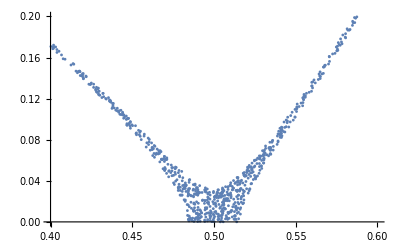
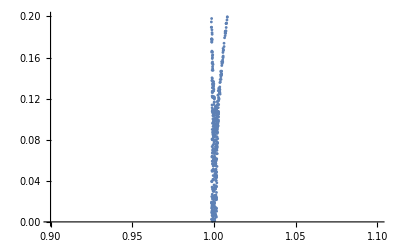
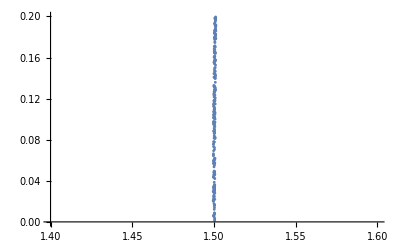

```mathematica
{FrontierInstaReg[2,RandTrLinLower[10000,1000,{.4,.6},{0,.2}] ,{0.4,.6},{0,.2}],
FrontierInstaReg[4,RandTrLinLower[10000,2000,{0.97,1.03},{0,.2}] ,{0.9,1.1},{0,.2}],
FrontierInstaReg[5,RandTrLinLower[10000,2000,{1.49,1.53},{0,.2}] ,{1.4,1.6},{0,.2}]}
```

It appears that the only tongue that doesn’t reach the α axis at a zero angle is the first one, which arrives to the axis at an angle. The first tongue has a non zero angle at its end, whereas the other tongues are proper cusps.
This means that for small values of k, its more probable that the lower equilibrium is unstable for Ω close to 2ω, less probable for Ω close to ω and much less probable for the following values associated to the half integers.

### Motion near the instability region

Let us finally see what the orbits look like, for values of α and k inside and outside the instability region:

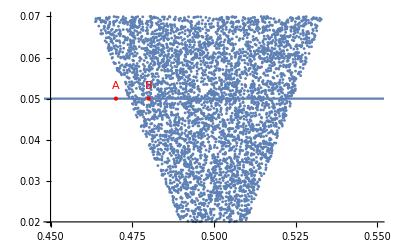

```mathematica
pts = Union[pts,RandTrLinLower[10000,400,{.45,.55},{.02,.07}]  ];
A={.47,.05};
B={.48,.05};
Show[InstaReg[pts,{.45,.55},{.02,.07}],Plot[.05,{x,.4,.6}],Graphics[{PointSize[Large],Red,Text["A",A+{0,0.003}],Point[A],Text["B",B+{0,0.003}], Point[B] }]]
```

Here is Point A, outside the instability region.

```mathematica
gorbA0 = GOrbPSMLower[ {0, 0.001} , 500 , A , 400 , {{-0.22,.22}, {-.22,.22}} ];
gorbA1 = GOrbPSMLower[ {0, 0.02} , 500 , A , 400 , {{-0.5,.5}, {-.5,.5}} ];
gorbA2 = GOrbPSMLower[ {0, 0.05} , 500 , A , 400 , {{-0.5,.5}, {-.5,.5} } ];
gorbA3 = GOrbPSMLower[ {0, 0.1} , 1000 , A , 400 , {{-0.5,.5}, {-.5,.5} } ];
gorbA4 = GOrbPSMLower[ {0,-0.2} , 1000 , A , 400 , {{-0.5,.5}, {-.5,.5} } ];
```

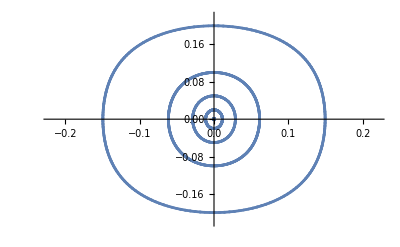

```mathematica
Show[ gorbA0,gorbA1,gorbA2,gorbA3,gorbA4]
```

We can clearly see that the point is elliptic, as expected.

Whereas, for point B, inside the unstable region:

```mathematica
gorbB0 = GOrbPSMLower[ {0, 0.001} , 1000 , B , 200 , {{-0.3,.3}, {-.3,.3}} ];
gorbB1 = GOrbPSMLower[ {0, 0.05} , 1000 , B , 200 , {{-0.5,.5}, {-.5,.5}} ];
gorbB2 = GOrbPSMLower[ {0, 0.05} , 500 , B , 200 , {{-0.5,.5}, {-.5,.5} } ];
gorbB3 = GOrbPSMLower[ {0, 0.1} , 1000 , B , 200 , {{-0.5,.5}, {-.5,.5} } ];
gorbB4 = GOrbPSMLower[ {0.05, 0} , 1000 , B , 200 , {{-0.5,.5}, {-.5,.5} } ];
```

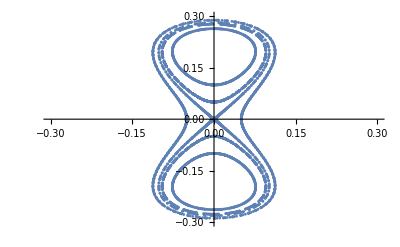

```mathematica
Show[ gorbB0,gorbB1,gorbB2,gorbB3,gorbB4]
```

The fixed point is hyperbolic. Two sets of orbits of period 2 have been created, and a periodic point of period 2.

Finally, here is an actual simulation of the pendulum, using the last parameters of point B.

```mathematica
motion[{0,0.01},B,{.01,1000},1000]
```

## Upper Equilibrium

## Functions

### Functions to build the stability region

```mathematica
AlgoLC= Compile[  {{αk,_Real,1},  h  ,  {txu,_Real,1}  }  ,{h+txu⟦1⟧,txu⟦2⟧+h (txu⟦3⟧+1/2 h txu⟦2⟧ (αk⟦1⟧^2-Cos[txu⟦1⟧] αk⟦2⟧)),txu⟦3⟧+h (txu⟦2⟧+1/2 h txu⟦3⟧) (αk⟦1⟧^2-Cos[h/2+txu⟦1⟧] αk⟦2⟧)}]
```

CompiledFunction[…]

```mathematica
SolEqVarC=Compile[{{αk,_Real,1},{ndiv,_Integer},{xv,_Real,1}},
     Drop[     Nest[ AlgoLC[ αk,  (2Pi)/ndiv ,#]&, Prepend[xv,0], ndiv] ,  1] ]
```

CompiledFunction[…]

```mathematica
LinPSMC[ ak_ , ndiv_]:={  SolEqVarC[ak,ndiv,{1,0}]  ,  SolEqVarC[ak,ndiv,{0,1}]  }
```

```mathematica
TrLin[αk_,ndiv_]:=Abs[Tr[LinPSMC[αk,ndiv]]]
```

```mathematica
αkTrLin[{a_,k_} ,ndiv_]:= { a , k, TrLin[{a,k},ndiv] }
```

```mathematica
sel[lst_]:=Select[lst,#[[-1]]<=2&]
```

```mathematica
Sez[lst_]:=Map[Drop[#,-1]&,sel[lst]]
```

```mathematica
RandTrLin[npts_,ndiv_,αint_, kint_]:=ParallelTable[αkTrLin[{RandomReal[αint],RandomReal[kint]},ndiv],npts]
```

```mathematica
StaReg[lst_,αint_, kint_]:=ListPlot[(Drop[#1,-1]&)/@sel[lst],PlotRange->{αint,kint},PlotStyle->PointSize[0.005]]
```

### Functions for the period shift map (or Poincaré Map)

```mathematica
AlgoC= Compile[  {{αk,_Real,1},  h  ,  {tθv,_Real,1}  }  ,{Mod[h+tθv⟦1⟧,2 π],Mod[tθv⟦2⟧+h (tθv⟦3⟧+1/2 h (-αk⟦1⟧^2+Cos[tθv⟦1⟧] αk⟦2⟧) Sin[tθv⟦2⟧]),2 π],tθv⟦3⟧+h (-αk⟦1⟧^2+Cos[h/2+tθv⟦1⟧] αk⟦2⟧) Sin[tθv⟦2⟧+1/2 h tθv⟦3⟧]}]
```

CompiledFunction[…]

```mathematica
PSMC=Compile[{{αk,_Real,1},{ndiv,_Integer},{θv,_Real,1} },
     Drop[ Nest[ AlgoC[ αk,  (2Pi)/ndiv ,#]&, Prepend[θv,0], ndiv] ,  1] ]
```

CompiledFunction[…]

```mathematica
OrbPSMC[θv_,nit_,αk_,ndiv_]:= NestList[PSMC[αk,ndiv,#]&,θv,nit]
```

Here too, allow the possibility of changing the PlotRange:

```mathematica
GOrbPSM[θv_,nit_,αk_,ndiv_,plrg_]:= ListPlot[ OrbPSMC[θv,nit,αk,ndiv], PlotRange->plrg,PlotStyle->PointSize[.005]]
```

## Analysis of the stability tongues

Let us plot the stability region:

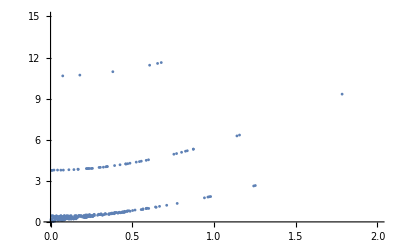

```mathematica
pts = RandTrLin[50000,800,{0,2},{0,15}]  ;
StaReg[ pts,{0,2},{0,15}  ]
```

For k=0 the equations that determine the trace of the linearization become x^(..)=+α^2x with initial conditions (x(0),ẋ(0)) = (1,0) and (0,1) whose solutions are 
( x(t)=x_0cosh(αt)+v_0/αsinh(αt) ; v(t)=-αx_0sinh(αt)+v_0cosh(αt) ) 
Hence the Trace is 2cosh(2πα) which has modulus ≥2. 
Hence there are no contact points on the α axis. 
We can deduce that for all values of (α,k) with k sufficiently close to zero the upper equilibrium remains unstable.

### How many tongues are there?

Let us plot the absolut value of the trace of the linearization for constant values of α close to zero.

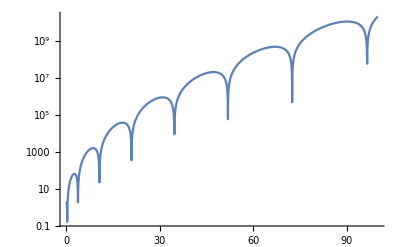

```mathematica
LogPlot[TrLin[{α,x},5000],{x,0,100},Ticks->{Range[0,100,10],{0,2,100,10000,10^6,10^8}}]
```

We have plotted the absolute value of the trace of the linearization for a fixed α=0.001. Since the plot was not easily readable here is shown the logplot. To each of these downward cusps corresponds a stability tongue. As we will see, these actually touch the axis, and being a continuous curve, this means that the trace of the linearization is less than two in a whole region, which gets smaller and smaller as k grows.
Let us highlight as red segments such values of k:

```mathematica
α=0.01;
line = Map[{α,#}&,Range[0,25,0.0001]];
selected =ParallelMap[Drop[#,{1,3,2}]&,sel[Map[αkTrLin[#,1000]&,line]]];
selected = Map[Append[#,2]&,selected];
```

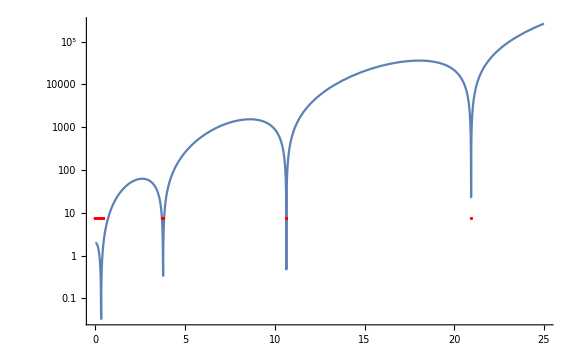

```mathematica
Show[LogPlot[TrLin[{α,k},400],{k,0,25},Ticks->{Range[0,25,5],Automatic}],ListPlot[selected,PlotStyle-> Red,PlotRange->All,PlotStyle->PointSize[0.2],ImageSize->Large]]
```

From these plots, there appear to be infinitely many stability tongues, getting smaller and smaller as k increases. Every downwards cusp corresponds to a stability tongue. There seem to be an infinite amount of them, and  the absolute val of the trace seems to grow exponentially, making the tips of the stability tongues thinner and thinner.

Moreover, an interesting thing to notice is that as α tends to 0, the lower and upper equilibrium have the same stability. This is because the dynamics became the same, except for a shift in time of π/2. The fact that they have the same stability can also be seen analitically:

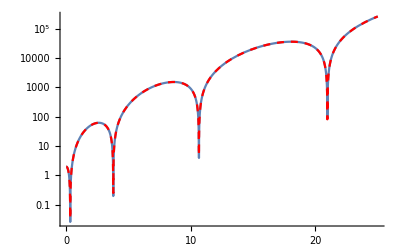

```mathematica
Show[LogPlot[TrLin[{α,k},800],{k,0,25},Ticks->{Range[0,25,5],Automatic}],LogPlot[TrLinLower[{α,k},800],{k,0,25},Ticks->{Range[0,25,5],Automatic},PlotStyle->{Red,Dashed}]]
```

In red is the absolute value of the trace of the linearization for the lower equilibrium.

### Motion near the stability region

Let us finally see what the orbits look like, for values of α and k inside and outside the first stability region:

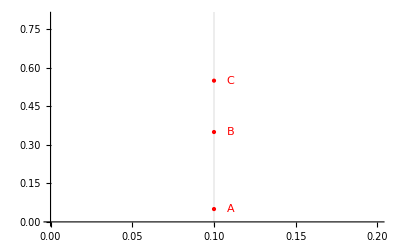

```mathematica
Show[
ListPlot[pts, PlotRange->{{0,0.2},{0,.8}}],Graphics[{PointSize[Large],Red,Text["A",{.11,.05}],Point[{.1,.05}],Text["B",{.11,.35}],Point[{.1,.35}],Text["C",{.11,.55}], Point[{.1,.55}] }],GridLines->{{.1},{}}]
```

Point A (k=0.1 , under the tongue)

```mathematica
gorbA0 = GOrbPSM[ {Pi, 0.001} , 500 , {0.1, 0.05} , 400 , {{Pi-0.2,Pi+0.2}, {-.05,.05} } ];
gorbA1 = GOrbPSM[ {Pi, -0.001} , 500 , {0.1, 0.05} , 400 , {{Pi-1,Pi+1}, {-.2,.2} } ];
gorbA2 = GOrbPSM[ {Pi, 0.03} , 500 , {0.1,0.05} , 400 , {{-0.5,.5}, {-.5,.5} } ];
gorbA3 = GOrbPSM[ {Pi, 0.1} , 1000 , {0.1,0.05} , 400 , {{-0.5,.5}, {-.5,.5} } ];
gorbA4 = GOrbPSM[ {Pi,-0.03} , 500 , {0.1,0.05} , 400 , {{-0.5,.5}, {-.5,.5} } ];
gorbA5 = GOrbPSM[ {Pi,-0.1} , 1000 , {0.1,0.05} , 400 , {{-0.5,.5}, {-.5,.5} } ];
```

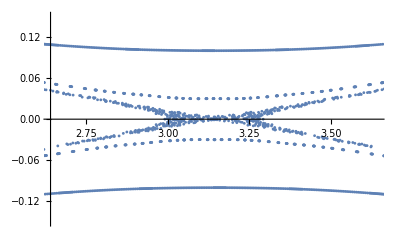

```mathematica
Show[ gorbA0,gorbA1,gorbA2,gorbA3,gorbA4,gorbA5]
```

The fixed point is hyperbolic. Two sets of orbits of period 2 have been created, and a periodic point of period 2.

Point B (k = 0.1 , inside the stability tongue)

```mathematica
gorbB0 = GOrbPSM[ {Pi, 0.001} , 500 , {0.1, 0.35} , 200 , {{Pi-0.2,Pi+0.2}, {-.013,.013} } ];
gorbB1 = GOrbPSM[ {Pi, 0.002} , 500 , {0.1, 0.35} , 200 , {{Pi-1,Pi+1}, {-.2,.2} } ];
gorbB2 = GOrbPSM[ {Pi,0.005} , 500 , {0.1,0.35} , 200 , {{-0.5,.5}, {-.5,.5} } ];
gorbB3 = GOrbPSM[ {Pi,0.01} , 1000 , {0.1,0.35} , 200 , {{-0.5,.5}, {-.5,.5} } ];
```

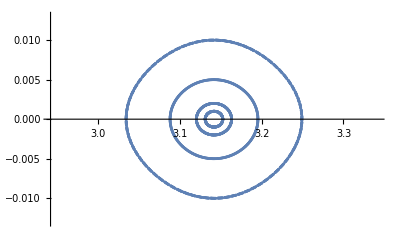

```mathematica
Show[ gorbB0,gorbB1,gorbB2,gorbB3]
```

```mathematica
gorbC0 = GOrbPSM[ {Pi, 0.001} , 500 , {0.1, 0.55} , 200 , {{Pi-1,Pi+1}, {-1,1} } ];
gorbC1 = GOrbPSM[ {Pi, -0.001} , 500 , {0.1, 0.55} , 200 , {{Pi-1,Pi+1}, {-.2,.2} } ];
gorbC2 = GOrbPSM[ {Pi,0.03} , 500 , {0.1,0.55} , 200 , {{-0.5,.5}, {-.5,.5} } ];
gorbC3 = GOrbPSM[ {Pi,0.1} , 500 , {0.1,0.55} , 200 , {{-0.5,.5}, {-.5,.5} } ];
gorbC4 = GOrbPSM[ {Pi,-0.03} , 500 , {0.1,0.55} , 400 , {{-0.5,.5}, {-.5,.5} } ];
gorbC5 = GOrbPSM[ {Pi,-0.1} , 500 , {0.1,0.55} , 400 , {{-0.5,.5}, {-.5,.5} } ];
```

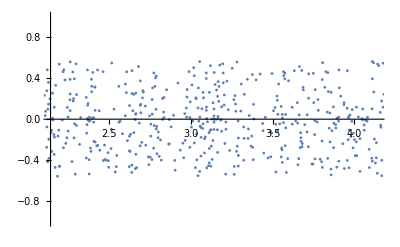

```mathematica
Show[ gorbC0,gorbC1,gorbC2,gorbC3,gorbC4,gorbC5]
```

```mathematica
motion[{Pi,0.01},{.1,.55},{.01,100},500]
```

For the second tongue what happens is:

$Aborted

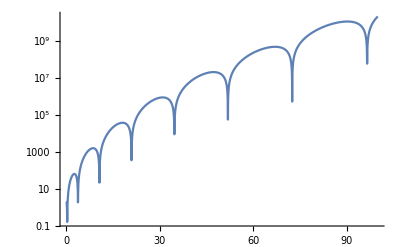

```mathematica
Manipulate[ 
GOrbPSM[{Pi,-0.01},500,{0.1,k},400,{{Pi-0.00005,Pi+0.00005},{-.012,.012}}] ,
{k,3.77,3.82,0.001}]
```